# Stellar Evolution Simulator Reese Danzer & Karthik Boyareddygari

## Output:

```mathematica
interface[]
```

## Main Code:

```mathematica
SetDirectory[NotebookDirectory[]];
oneMSunData=Import["One Solar Mass.txt","Table"];
oneMSun=Dataset[Table[
<|"Step"->oneMSunData[[i,1]],"Age"->oneMSunData[[i,2]],"Mass"->oneMSunData[[i,3]],"Luminosity"->10^oneMSunData[[i,4]],"Radius"->10^oneMSunData[[i,5]],"T_s"->10^oneMSunData[[i,6]],"T_c"->10^oneMSunData[[i,7]],"ρ_c"->10^oneMSunData[[i,8]],"P_c"->10^oneMSunData[[i,9]],"R_He"->oneMSunData[[i,27]],"R_C"->oneMSunData[[i,28]],"R_O"->oneMSunData[[i,29]]|>,
{i,Length[oneMSunData]}]
];
```

```mathematica
interface[]:=
DynamicModule[{
maxStep=Length[oneMSunData],
maxRadius=oneMSun[Max,"Radius"],
maxLuminosity=oneMSun[Max,"Luminosity"],
maxTSurface=oneMSun[Max,"T_s"],
color,radius,surfaceTemp,centerTemp,luminosity
},
Manipulate[
color=fancyInterpolate[step,"Radius"]^-1;
radius=fancyInterpolate[step,"Radius"];
luminosity=fancyInterpolate[step,"Luminosity"];
surfaceTemp=fancyInterpolate[step,"T_s"];
centerTemp=fancyInterpolate[step,"T_c"];
(*This will be the list of changing variables to be used below, because if we just slap the commands in themselves it will get really cluttered really fast.*)
GraphicsGrid[{
{Graphics3D[{Hue[0.2],Tooltip[Sphere[{0,0,0} ,radius]]},Background->Black,Boxed->False,PlotRange->maxRadius],
(*The Sphere Graphic*)
Panel[Graphics[PlotRange->{{maxTSurface,0},{0,maxLuminosity}},Axes->True,GridLines->Automatic, Background->Black,AxesStyle->Directive[Red],AxesLabel->{"T_s","L⊙"},Epilog->{Darker[Yellow,0.2],PointSize->0.04,Point[{surfaceTemp,luminosity}]}],Background->Black]},
(*The HR Diagram*)
{Graphics[{Hue[0.02],Tooltip[Disk[{0,0},1]],Hue[0.15],Tooltip[Disk[{0,0},1/step]]},PlotRange->1.1,Background->Darker[Gray,0.75]],
(*The Internal Diagram*)
Panel[Graphics[{FontSize->16, Text["Surface Temperature: "<>ToString[NumberForm[Round[surfaceTemp],DigitBlock->3]]<>"°K"<>"\nCenter Tempurature: "<>ToString[NumberForm[Round[centerTemp],DigitBlock->3]]<>"°K"<>"\nRadius: "<>ToString[NumberForm[radius,DigitBlock->3,NumberSeparator->","]]<>" R⊙"<>"\nLuminosity: "<>ToString[NumberForm[luminosity,DigitBlock->3,NumberSeparator->","]]<>" L⊙"<>"\nMagnitude: "<>ToString[step]]}]]}
(*The Text Readouts*)
},
ContentSelectable->False,
(*So they don't get their grubby hands on our nice animation.*)
ImageSize->Full
],
{step,11,maxStep-11},ContentSize->{600,600}]
]
```

```mathematica
fancyInterpolate[step_,qty_]:=
Module[{ageFunction=Interpolation[Normal[oneMSun[All,"Age"]]]},
Return[
Interpolation[
connect[{Normal[oneMSun[Round[step-10];;Round[step+10],"Age"]],
Normal[oneMSun[Round[step-10];;Round[step+10],qty]]}],
ageFunction[step]]
];
]
```

```mathematica
connect[listoflist_]:=(*assume that all lists in listoflist are of the same length because we are inputting them*)
Module[{length=Length[listoflist[[1]]],lengthmain=Length[listoflist],final},
final=Table[listoflist[[k,i]],{i,1,length},{k,1,lengthmain}];(*create a list of length lists each being lengthmain elements long*)
Return[final]
]
```

```mathematica
alter[data_]:=
Module[{association},
association=<|"Step"->data[[1]],"Age"->data[[2]],"Mass"->data[[3]],"Luminosity"->10^data[[4]],"Radius"->10^data[[5]],"T_s"->10^data[[6]],"T_c"->10^data[[7]],"ρ_c"->10^data[[8]],"P_c"->10^data[[9]],"R_He"->data[[27]],"R_C"->data[[28]],"R_O"->data[[29]]|>;
Return[association];
]
```

## Datasets:

```mathematica
Dynamic[oneMSun]
```

## Variable Explanations:

Age: A number from 0 to 1 that represents the position the data point represents in the star’s life.
Mass: Mass of the star in M⊙.
Radius: Radius of the star, in R⊙.
Luminosity: Luminosity of the star, in L⊙.

## Data Graphs:

## One Msun:

#### Age

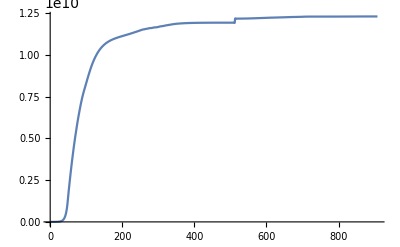

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"Age"]]][x],{x,1,908},PlotRange->Full]
```

#### Mass

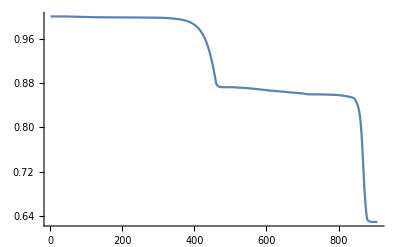

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"Mass"]]][x],{x,1,908},PlotRange->Full]
```

#### Radius

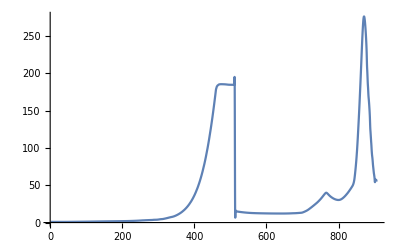

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"Radius"]]][x],{x,1,908},PlotRange->Full]
```

#### Luminosity

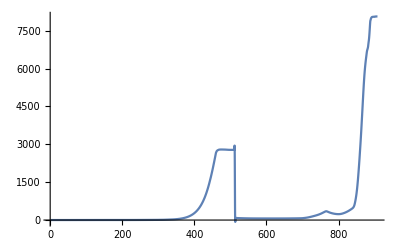

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"Luminosity"]]][x],{x,1,908},PlotRange->Full]
```

#### Surface Tempurature

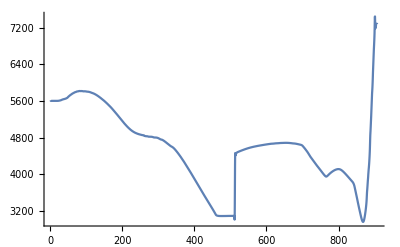

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"T_s"]]][x],{x,1,908},PlotRange->Full]
```

#### Center Tempurature

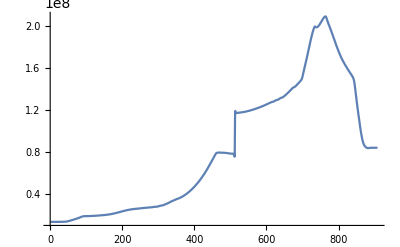

```mathematica
Plot[Interpolation[Normal[oneMSun[All,"T_c"]]][x],{x,1,908},PlotRange->Full]
```